```mathematica
Subscript[a_,b_]:=Part[a,b];
SetOptions[#,{Joined->True,Frame->True,LabelStyle->{FontFamily->"Arial",16,GrayLevel[0]},FrameTicksStyle->{Thickness[0.5]},FrameStyle->Directive[Black,Thickness[0.005]]}]& /@ {ListPlot,ListLogPlot,ListLogLogPlot};
SetOptions[#,{Frame->True,LabelStyle->{FontFamily->"Arial",16,GrayLevel[0]},FrameTicksStyle->{Thickness[0.5]},FrameStyle->Directive[Black,Thickness[0.005]]}]& /@  {Plot,LogPlot,DensityPlot};
```

```mathematica
ClearAll[ν,λ];
c=3 10^8;
TBP=0.32;
fs=10^-15; ps=10^-12; nm=10^-9;μm=10^-6;THz=10^12;
ν[λ_]:=c/λ;λ[ν_]:=c/ν;
```

Example case: pump pulse duration 150 fs, demand equally fine representation in both domains with ~1024 points.

```mathematica
τpump=150 fs;
νpump=ν[1000 nm];
νsignal=ν[1500 nm];
νidler=νpump-νsignal;
N@λ[νidler]/μm;
```

```mathematica
tspan=N@60τpump;
νres=1/tspan;
νspan=N@ 60 TBP/τpump;
tres=1/νspan;
```

```mathematica
Ld[n_]:=Log[2,n];
```

```mathematica
NptsCpldWave=2^(Round@Log[2,tspan/tres])
```

1024

```mathematica
tspan/ps
tres/fs
νspan/THz
νres/THz
```

9.

7.8125

128.

0.111111

```mathematica
totalνspan=(νpump+νspan/2)-(νidler-νspan/2);
```

```mathematica
NptsUPPE=2^(Round@Log[2,totalνspan/νres])
```

4096

```mathematica
NptsUPPE Ld[NptsUPPE]
```

49152

```mathematica
3 NptsCpldWave Ld[NptsCpldWave]
```

30720

It should be quite clear that the computational effort is quite similar for both algorithms.

```mathematica
releff[τpump_]:=Module[{tspan=N@60τpump,νspan=N@ 60 TBP/τpump,νres,tres,totalνspan,NptsCpldWave,NptsUPPE},
νres=1/tspan;
tres=1/νspan;
NptsCpldWave=2^(Round@Log[2,tspan/tres]);
totalνspan=(νpump+νspan/2)-(νidler-νspan/2);
NptsUPPE=2^(Round@Log[2,totalνspan/νres]);
{{N@τpump/ps,NptsUPPE Ld[NptsUPPE]/3 10^-4},{N@τpump/ps,3 NptsCpldWave Ld[NptsCpldWave]/3 10^-4}}]
```

```mathematica
releff[100fs]
```

{{0.1,1408/1875},{0.1,128/125}}

Now let’s look into how this changes with pulse duration

```mathematica
For[τx=1;res={},τx<=4,τx+=0.1,res=Append[res,releff[10^τx fs]]]
```

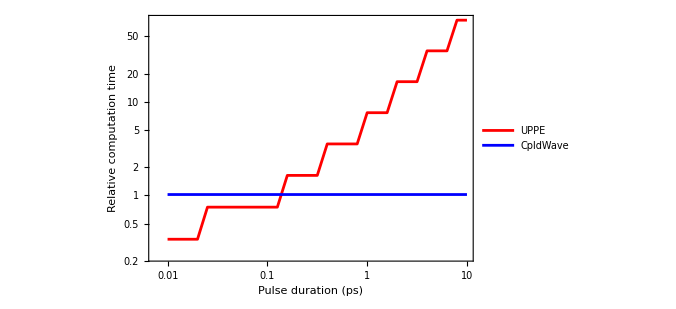

```mathematica
ListLogLogPlot[{Subscript[(resᵀ), 1],Subscript[(resᵀ), 2]},PlotStyle->{Red,Blue},PlotLegends->Placed[{"UPPE","CpldWave"},{0.2,0.8}],ImageSize->500,FrameLabel->{"Pulse duration (ps)","Relative computation time"}]
```

So, UPPE appears superior for pulses shorter than 100 fs or so, but coupled waves are expected to fare much better for ps pulses.

Now let’s modify this a little bit by demanding that we need at least a 10 ps time interval to account for group velocity mismatch.

```mathematica
releff2[τpump_]:=Module[{tspan=Max[N@60τpump, 10 ps],νspan=N@ 60 TBP/τpump,νres,tres,totalνspan,NptsCpldWave,NptsUPPE},
νres=1/tspan;
tres=1/νspan;
NptsCpldWave=2^(Round@Log[2,tspan/tres]);
totalνspan=(νpump+νspan/2)-(νidler-νspan/2);
NptsUPPE=2^(Round@Log[2,totalνspan/νres]);
{{N@τpump/ps,NptsUPPE Ld[NptsUPPE]/3 10^-4},{N@τpump/ps,3 NptsCpldWave Ld[NptsCpldWave]/3 10^-4}}]
```

```mathematica
For[τx=1;res={},τx<=4,τx+=0.1,res=Append[res,releff2[10^τx fs]]]
```

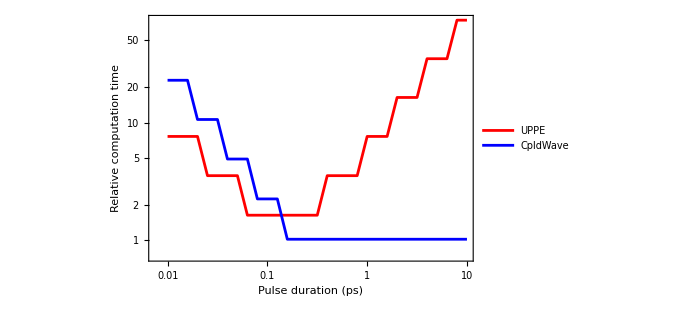

```mathematica
ListLogLogPlot[{Subscript[(resᵀ), 1],Subscript[(resᵀ), 2]},PlotStyle->{Red,Blue},PlotLegends->Placed[{"UPPE","CpldWave"},{0.2,0.8}],ImageSize->500,FrameLabel->{"Pulse duration (ps)","Relative computation time"}]
```

Now, UPPE still has an edge below 100 fs, but this is really only a factor 3 at best. At pulse durations above 1 ps, coupled wave eqns. are clearly superior.